```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Github\Diffusion-Lattice-Distribution-Set-Theory

```mathematica
Get["./base_package/SOHR_base.m"]
```

# A⇌_k_1^k_1B type reaction network

```mathematica
PathProbV = GetPathwayProbabilityVector[5];
```

```mathematica
PathProbV//MatrixForm
```

(ⅇ^(-k1 t)
(ⅇ^(-k2 t) k1)/(k1-k2)+(ⅇ^(-k1 t) k1)/(-k1+k2)
(ⅇ^(-k3 t) k1 k2)/((k1-k3) (k2-k3))+(ⅇ^(-k1 t) k1 k2)/((-k1+k2) (-k1+k3))+(ⅇ^(-k2 t) k1 k2)/((k1-k2) (-k2+k3))
(ⅇ^(-k4 t) k1 k2 k3)/((k1-k4) (k2-k4) (k3-k4))+(ⅇ^(-k1 t) k1 k2 k3)/((-k1+k2) (-k1+k3) (-k1+k4))+(ⅇ^(-k2 t) k1 k2 k3)/((k1-k2) (-k2+k3) (-k2+k4))+(ⅇ^(-k3 t) k1 k2 k3)/((k1-k3) (k2-k3) (-k3+k4))
(ⅇ^(-k5 t) k1 k2 k3 k4)/((k1-k5) (k2-k5) (k3-k5) (k4-k5))+(ⅇ^(-k1 t) k1 k2 k3 k4)/((-k1+k2) (-k1+k3) (-k1+k4) (-k1+k5))+(ⅇ^(-k2 t) k1 k2 k3 k4)/((k1-k2) (-k2+k3) (-k2+k4) (-k2+k5))+(ⅇ^(-k3 t) k1 k2 k3 k4)/((k1-k3) (k2-k3) (-k3+k4) (-k3+k5))+(ⅇ^(-k4 t) k1 k2 k3 k4)/((k1-k4) (k2-k4) (k3-k4) (-k4+k5)))

```mathematica
PPV = PathProbV;
For[i=Length[PPV],i≥1,i--,
For[j=i-1,j≥1,j--,PPV⟦i⟧=CalculateLimit[PPV⟦i⟧,j+1,j]]
];
```

```mathematica
PPV//MatrixForm
```

(ⅇ^(-k1 t)
ⅇ^(-k1 t) k1 t
1/2 ⅇ^(-k1 t) k1^2 t^2
1/6 ⅇ^(-k1 t) k1^3 t^3
1/24 ⅇ^(-k1 t) k1^4 t^4)

## Has pattern of 1/(n!)ⅇ^(-k_1 t) k_1^n t^n, this is exactly the Poisson distribution Pr(N_t=n) =f(n; λt) =e^-λt/(n!)(λt)^n

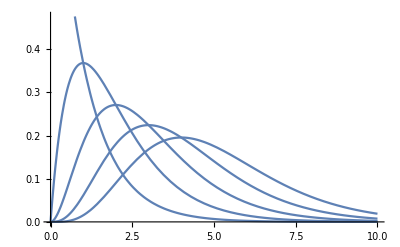

```mathematica
Plot[PPV/.k1->1.0,{t,0,10}]
```

```mathematica
(*Names[$Context<>"*"]*)
```